```mathematica
areaOfDetector=(19/1000)^2; (* 19mm x 19mm *)
areaOfAperture=(16*(4+Pi))/1000^2; (* 8mm x 16mm with rounded edges *)
detectorFieldOfViewDiameter=2°;
detectorFieldOfViewSolidAngle=2*Pi*(1-Cos[detectorFieldOfViewDiameter/2]);
```

```mathematica
directory="/home/sidney/Repositories/github/MitsubaARCF/arcf-model";
```

## Process Irradiance Measurement

```mathematica
irradianceFilename=FileNameJoin[{directory,"arcf-irradiance.m"}];

irradiance=Block[{detector},Get[irradianceFilename];detector];

signalIrradiance=Mean[Flatten[irradiance]];

signalIrradiancePerfect=areaOfAperture/areaOfDetector;

(* 'powerPerAreaIrradiance' [W/m^2] should be equal to the exitance of the emitter. *)
powerPerAreaIrradiance=signalIrradiance*areaOfDetector/areaOfAperture;
```

```mathematica
Print["Dimensions: ",Dimensions[irradiance]]
Print["signalIrradiance: ",signalIrradiance]
Print["powerPerAreaIrradiance: ",powerPerAreaIrradiance]
```

Dimensions: {256,256}

signalIrradiance: 0.3166500422681981726928752197

powerPerAreaIrradiance: 1.000395419512622098185281788

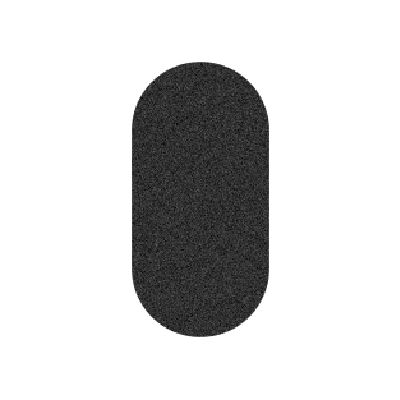

```mathematica
ArrayPlot[irradiance,PlotRange->All]
```

```mathematica
ListPlot3D[irradiance,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[LowpassFilter[irradiance,1/10],PlotRange->All]
```

-Graphics3D-

## Process Radiance Measurement

```mathematica
radianceFilename=FileNameJoin[{directory,"../arcf-model-bug/arcf-ok.m"}];
radianceFilename=FileNameJoin[{directory,"../scenes/test-fieldfocus.m"}];
radianceFilename=FileNameJoin[{directory,"arcf-radiance.m"}];

radiance=Block[{detector},Get[radianceFilename];detector];

signalRadiance=Mean[Flatten[radiance]];
```

```mathematica
Print["Dimensions: ",Dimensions[irradiance]]
Print["signalRadiance: ",signalRadiance]
```

Dimensions: {256,256}

signalRadiance: 0.00009779219585193106567976101857

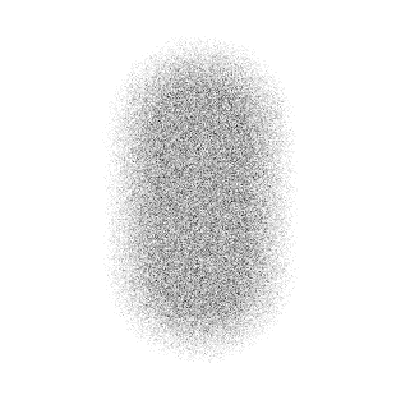

```mathematica
ArrayPlot[radiance,PlotRange->All]
```

```mathematica
ListPlot3D[radiance,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[LowpassFilter[radiance,1/10],PlotRange->All]
```

-Graphics3D-

## Calclulate BSDF

```mathematica
bsdfPerfect=N[1/Pi,30]
signalRadiancePerfect=(1/π)*(signalIrradiancePerfect)*(detectorFieldOfViewSolidAngle*Cos[45°])//N
bsdfEstimate=(signalRadiance/signalIrradiance)/(detectorFieldOfViewSolidAngle*Cos[45°])
```

0.318309886183790671537767526745

0.0000681768

0.4564004480789150641674225922

```mathematica
signalRadiance/signalRadiancePerfect
```

1.43439